## §5. Ряды Лорана

### 5.1. Ряды Лорана. Теорема Лорана.

Рядом Лорана называется ряд

f(z)=∑_(n=-∞)^∞ (c_n(z-z_0))^n

при этом ряд

f_2(z)=∑_(n=-∞)^-1 (c_n(z-z_0))^n

называется главной частью ряда Лорана, а ряд

f_3(z)=∑_(n=0)^∞ (c_n(z-z_0))^n

- правильной частью. Если

lim_(n→∞) (|c_-n|)^(1/n)=r<R=1/(lim_(n→∞) (|c_n|)^(1/n))

то областью сходимости ряда (1) является кольцо K={ z| 0≤ r< |z-z_0|<R}. В этом кольце К сумма ряда f(z)=f_1(z)+f_2(z) является функцией аналитической, причем коэффициенты ряда c_n связаны с функцией f(z) посредством формул

c_n=1/(2π ⅈ)∫_(|z-z_0|=r') (f(z))/(z-z_0)^(n+1)ⅆz,     где r<r'<R, n+1>0

Причем если функция f(z) аналитичная в кольце |z-z_0|=r', то коэффициенты разложения будут вычисляться по формуле:

c_n=1/(n!)(ⅆ^n/(ⅆ z^n)f)(z_0)

Т е о р е м а  Л о р а н а. Если функция f(z) аналитична в кольце 0≤ r< |z-z_0|<R, то в этом кольце она единственным образом представима в виде ряда Лорана (1), коэффициенты которого вычисляются по формулам (2).

В данном разделе решение будем приводить методами функционального и алгоритмического программирования, в отличии от традиционных рутинных “бумажных” решений.

Использование подобных методов позволяет оптимальнее решать задачи, в чем и заключается преимущество Mathematica.

##### Пример №12.352

Найти все разложения указанной функции в ряд Лорана по степеням z-z_0 и установить области сходимости полученных разложений:

f(z)=1/(z(z-1)),  z_0=1

Сначала рассмотрим детальное решение данной задачи. Затем усложним ее, так как на исходном примере нельзя отследить все этапы, необходимые для понимания общего алгоритма. И потом, наконец, составим программу разложения функций в ряд Лорана.

Запишем функцию:

```mathematica
f[z_]:=1/(z(z-1))
```

Из структуры функции видно, что её аналитичность  нарушается в точках z_0=1, z_1=0. Следовательно функция будет аналитична в кольцах: 1) 0< |z-1|< 1  2) |z-1| >1

Изобразим точки z_1 и z_2, а также контуры интегрирования r1 и r2, которые находятся соответственно в кольце 1) и 2):

```mathematica
Graphics[{Circle[{0,0},0.3],Circle[{1,0},0.6],Circle[{1,0},2],PointSize[Large],Point[{0,0}],Point[{1,0}],Text[r1,{0.6,0.6}],Text[r2,{2,2}] ,Text[γ,{0.3,0.3}]   },PlotRange->{{-3,3},{-3,3}},Axes->True]
```

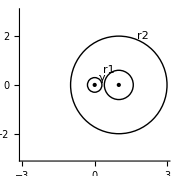

Для того чтобы найти разложение в ряд Лорана в окрестности точки z_0, достаточно воспользоваться уже известной нам функцией Series,о которой говорится в разделе Ряды Тейлора и которая имеет вид: Series[ f[z], {z,z_0,n}] :

```mathematica
Series[f[z],{z,1,5}]
```

1/(z-1)-1+(z-1)-(z-1)^2+(z-1)^3-(z-1)^4+(z-1)^5+O[z-1]^6

Получим выражение для n-ого коэффициента:

```mathematica
SeriesCoefficient[f[z],{z,1,n}]
```

Piecewise[{{1, n==-1}, {(-1)^(1+n), n≥0}, {0, True}}]

Запишем n-ый коэффициент как функцию от n. Это понадобится нам в дальнейшем:

```mathematica
c1[n_]:=Piecewise[{{(-1)^(n+1),n≥ -1},{0,n<-1}}]
```

Таким образом, мы получили разложение:

f(z)=∑_(n=-1)^∞ (-1)^(n+1)(z-1)^n   , при 0< |z-1| <1

Для того чтобы найти разложение в кольце|z-1| >1, воспользуемся формулой (2):

c_n=∮_(|z-1|=R) (f(z))/(z-1)^(n+1)ⅆz, где R>1

Согласно теореме Коши для многосвязной области имеем:

∮_(|z-1|=R) (f(z))/(z-1)^(n+1)ⅆz=∮_(|z-1|=r') (f(z))/(z-1)^(n+1)ⅆz+∮_(|z|=r') (f(z) ·z)/((z-1)^(n+1)·z)ⅆz, где 0<r'<1

Здесь первый интеграл есть разложение в ряд Лорана в кольце 0< |z-1|<1 и уже вычислен, а второй интеграл, исходя из интегральной формулы Коши, будет равен:

∮_(|z|=r') (f(z) ·z^u)/((z-1)^(n+1)·z^u)ⅆz=1/(u!)(ⅆ^(u-1)/(ⅆ z^(u-1))(f(z) ·z^u)/(z-1)^(n+1))(0), где u- кратность корня z=0  в уравнении Denominator[f(z)]=0

Теперь запишем функцию c2 от n:

```mathematica
c2[n_]:=Simplify[f[z] z/(z-1)^(n+1)]/.z->0
```

Протабулируем функцию c2(n)  на отрезке от -8 до 8

```mathematica
Table[{n,c2[n]},{n,-8,8}]
```

{{-8,1},{-7,-1},{-6,1},{-5,-1},{-4,1},{-3,-1},{-2,1},{-1,-1},{0,1},{1,-1},{2,1},{3,-1},{4,1},{5,-1},{6,1},{7,-1},{8,1}}

В нашем обозначении из (4) следует:

c_n=c_(1n)+c_(2n)

Отобразим множество вида { n, c_n }, -8≤ n≤ 8:

```mathematica
Table[{n,c1[n]+c2[n]},{n,-8,8}]
```

{{-8,1},{-7,-1},{-6,1},{-5,-1},{-4,1},{-3,-1},{-2,1},{-1,0},{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0}}

Как мы видим, коэффициенты при степени большей -2, равны 0.

Конечно, в нашем конкретном случае функция общего члена c(n) легко определяется, однако воспользуемся функцией FindSequenceFunction, которая, как следует из названия, находит функцию из последовательности. Она имеет следующую структуру: FindSequenceFunction[ { {n_-k,a_k}....{n_0,a_0}....{n_q,a_q}}, n]. Применим ее к последовательности, начинающейся при n=-2 и до n=-8.

```mathematica
FindSequenceFunction[Table[{n,c2[n]},{n,-8,-2}],n]
```

(-1)^(10+n)

Итак, запишем разложение в ряд Лорана в кольце |z-1| >1:

```mathematica
Sum[(z-1)^n(c1[n]+c2[n]),{n,-8,8}]
```

1/(-1+z)^8-1/(-1+z)^7+1/(-1+z)^6-1/(-1+z)^5+1/(-1+z)^4-1/(-1+z)^3+1/(-1+z)^2

В общем виде:

f(z)=∑_(n=2)^∞ (-1)^n/(z-1)^n, при  |z-1| >1

Рассмотрим более сложный пример.

##### Пример №2

Найти все разложения указанной функции в ряд Лорана по степеням z-z_0 и установить области сходимости полученных разложений:

f(z)=1/((z-2)^2(z+3)^3), z_0=-3

В данной задаче представлена более сложная функция с несколькими точками потери аналитичности разной кратности.

Запишем функцию:

```mathematica
f[z_]:=1/((z-2)^2(z+3)^3)
```

Для того чтобы найти кольца аналитичности, решим уравнение f[z]^-1=0 или просто приравняем знаменатель к 0. Для того чтобы получить знаменатель функции f(z), будем использовать опцию Denominator[ f[z] ]

```mathematica
sol=z/.Solve[Denominator[f[z]]==0,z]
```

{-3,-3,-3,2,2}

Следующим пунктом в нашем алгоритме будет определение кратности каждого корня. Воспользуемся тем же методом, что и в главе 1 параграфе 4 “Интегралы”. Там мы определяли кратность при помощи функции Counts[list]:

```mathematica
rul=Counts[sol]
```

<|-3→3,2→2|>

Теперь запишем функцию кратности i-ого корня:

```mathematica
sol=DeleteDuplicates[sol];
u[i_]:=sol[[i]]/.rul
```

Теперь нужно разделить комплексную плоскость на окружности. Изобразим графически:

```mathematica
Graphics[{Circle[{-3,0},3],Circle[{2,0},0.6],Circle[{-3,0},6],PointSize[Large],Point[{-3,0}],Point[{2,0}],Text[r1,{0.6,0.6}],Text[r2,{2,2}] ,Text[γ,{2.7,0.6}]   },PlotRange->{{-8,8},{-8,8}},Axes->True]
```

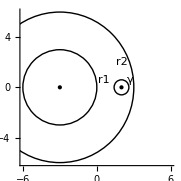

Для того чтобы аналитически определить кольца сходимости, поступим следующим образом: возьмем точку z_0-центр разложения и будем сравнивать расcтояние от нее до корней z_1....z_n. Наименьшее раcстояние будет соответствовать верхней границе первого кольца и нижней границе второго кольца, верхней же границе второго кольца будет соответствовать уже наименьшее раcстояние до следующего корня, и так далее. Составим множество границ колец, используя функцию Sort[ list ], которая располагает элементы list  в порядке возрастания. Сортировать же мы будем множество всех раcстояний от z_0 до z_i:

```mathematica
a=With[{z0=-3},Sort[Table[Abs[-z0+sol[[i]]],{i,1,Length[sol]}]]]
```

{0,5}

Первый элемент равен нулю - следовательно центр разложения z_0 совпадает с одним из корней.

Получили 2 кольца: 1) 0< |z+3|<5 и 2)|z+3| >5

Разложение в окрестности z_0 всегда можно отыскать с помощью функции Series:

```mathematica
Series[f[z],{z,-3,5}]
```

1/(25 (z+3)^3)+2/(125 (z+3)^2)+3/(625 (z+3))+4/3125+(z+3)/3125+(6 (z+3)^2)/78125+(7 (z+3)^3)/390625+(8 (z+3)^4)/1953125+(9 (z+3)^5)/9765625+O[z+3]^6

Получим формулу n-ого коэффициента:

```mathematica
c0=SeriesCoefficient[f[z],{z,-3,n}]
```

Piecewise[{{3/625, n==-1}, {2/125, n==-2}, {1/25, n==-3}, {5^(-5-n) (4+n), n≥0}, {0, True}}]

Составим функцию c_1(n)  - коэффициента разложения в кольце 1):

```mathematica
c1[k_]:=c0/.n->k
```

Итак, получили:

f(z)=∑_(n=-3)^∞ ((4+n)(z+3)^n)/5^(5+n), при 0< |z+3|<5

Разложение в кольце 2) |z+3| >5 будем искать аналогично формуле (4):

c_(2n)=1/(1!)ⅆ/ⅆz(f(z)(z-2)^2)/(z+3)^(n+1),z→ 2

Запишем выражение для коэффициента c_2(n):

```mathematica
c2[n_]:=D[Simplify[f[z](z-sol[[2]])^u[2]/(z+3)^(n+1)],{z,u[2]-1}]/.z->2
```

```mathematica
Table[{n,c2[n]},{n,-8,8}]
```

{{-8,500},{-7,75},{-6,10},{-5,1},{-4,0},{-3,-1/25},{-2,-2/125},{-1,-3/625},{0,-4/3125},{1,-1/3125},{2,-6/78125},{3,-7/390625},{4,-8/1953125},{5,-9/9765625},{6,-2/9765625},{7,-11/244140625},{8,-12/1220703125}}

Итак, теперь, для того чтобы найти разложение в кольце, внутренний контур которого охватывает все особые точки, нужно вычислить сумму коэффициентов c(n)=c_1(n)+c_2(n):

```mathematica
Sum[(z+3)^n(c1[n]+c2[n]),{n,-12,8}]
```

625000/(3+z)^12+109375/(3+z)^11+18750/(3+z)^10+3125/(3+z)^9+500/(3+z)^8+75/(3+z)^7+10/(3+z)^6+1/(3+z)^5

Найдем формулу коэффициента n:

```mathematica
c22[k_]:=FindSequenceFunction[Table[{n,c1[n]+c2[n]},{n,-12,-5}],j]/.j->k
```

```mathematica
c22[n]
```

-5^(-5-n) (4+n)

Из получившейся последовательности действий видно, что каждый раз при увеличении радиуса кольца разложения (выход за предел текущего кольца) общий коэффициент разложения будет увеличиваться на c_i(n).

В итоге, получили:

f(z)=(-∑)_(n=-∞)^-5((4+n)(z+3)^n)/5^(5+n), при |z+3| >5

f(z)=∑_(n=-3)^∞ ((4+n)(z+3)^n)/5^(5+n), при 0< |z+3|<5

##### Общий алгоритм

Проанализировав последовательность действий, создадим программный модуль разложения в ряд Лорана:

```mathematica
loranO[z_,expr_  ,z0_,r_,k_]:=Module[{sol,sol1,u,c0,c1},
c0[n_]:=Evaluate[SeriesCoefficient[expr,{z,z0,n}]];
sol1=z/.Solve[0<Abs[z-z0]<r&&Denominator[Simplify[TrigToExp[expr]]]==0,z];
c1[n_]:=0;
If[sol1≠ {},
sol=DeleteDuplicates[sol1];
u[i_]:=sol[[i]]/.Counts[sol1];
c1[n_]:=Sum[1/((u[i]-1)!)Limit[D[Simplify[expr(z-sol[[i]])^u[i]/(z-z0)^(n+1)],{z,u[i]-1}],z-> sol[[i]]],{i,1,Length[sol]}]];
Sum[(z-z0)^n(c0[n]+c1[n]),{n,-k,k}]]
```

Итак, данный модуль имеет следующую построчную структуру:

1. Запись коэффициента c0[n] разложения в ряд в окрестности z_0.

2. Поиск тех корней знаменателя, которые расположены не дальше r - кольца разложения, не включая корень z0.

3. В случае если множество корней не пустое множество, определение кратности каждого корня.

4. Вычисление коэффициентов c_i[n] по формуле (4).

5. Запись получившегося разложения.

Продемонстрируем пример работы:

##### Пример №12.354

```mathematica
loranO[z,1/((z-2)(z+3)),2,6,8]
```

15625/(-2+z)^8-3125/(-2+z)^7+625/(-2+z)^6-125/(-2+z)^5+25/(-2+z)^4-5/(-2+z)^3+1/(-2+z)^2

##### Пример №12.364

```mathematica
loranO[z,z/((z^2+1)^2),I,3,8]
```

-(112 ⅈ)/(-ⅈ+z)^8+48/(-ⅈ+z)^7+(20 ⅈ)/(-ⅈ+z)^6-8/(-ⅈ+z)^5-(3 ⅈ)/(-ⅈ+z)^4+1/(-ⅈ+z)^3

##### Пример № х

```mathematica
loranO[z,1/Sin[z],0,Pi+1,8]
```

-(2 π^6)/z^7-(2 π^4)/z^5-(2 π^2)/z^3-1/z+(1/6-2/π^2) z+(7/360-2/π^4) z^3+(31/15120-2/π^6) z^5+(127/604800-2/π^8) z^7

Созданную функцию будем использовать при необходимости в дальнейшем.

### 5.2. Характер изолированных особых точек

Точка z_0 называется правильной точкой для аналитической в области D функции f(z), если существует степенной ряд ∑_(n=0)^∞ c_n(z_0) (z-z_0)^n с радиусом сходимости r(z_0)>0 такой, что в общей части круга сходимости |z-z_0|<r(z_0) и области D сумма этого ряда ϕ_z_0(z) совпадает с f(z). Точки, не являющиеся правильными, называются особыми.

Точка z_0 называется изолированной особой точкой функции f(z) , если f(z)  - однозначная аналитическая функция в кольце 0< |z-z_0|<R, а z_0 - особая точка.

Аналогично, точка z_0=∞ называется изолированной особой точкой функции f(z), если f(z)  - однозначная аналитическая функция в кольце r< |z| <∞ и z=∞ - особая точка.

Изолированная особая точка z_0 функции f(z) называется:

Устранимой особой точкой, если существует конечный предел:

lim_(z→z_0) f(z)=a≠ ∞

Полюсом порядка m≥ 1, если для функции g(z)=(f(z))^-1 точка z_0 является нулем порядка m. Если z_0 - полюс, то

lim_(z→z_0) f(z)= ∞

Существенно особой если конечного предела не существует:

lim_(z→z_0) f(z)- не существует

##### Пример №12.382

Указать все конечные особые точки заданной ниже функции и определить их характер:

f(z)=1/((z^2+i)^3)

Запишем функцию:

```mathematica
f[z_]:=1/((z^2+I)^3)
```

Для того чтобы найти особые точки, решим уравнение Denominator[f[z]]=0:

```mathematica
sol=Flatten[Solve[Denominator[f[z]]==0,z]]
```

{z→-(-1)^(3/4),z→-(-1)^(3/4),z→-(-1)^(3/4),z→(-1)^(3/4),z→(-1)^(3/4),z→(-1)^(3/4)}

Мы получили 2 корня кратности 3. Для того чтобы избавиться от повторов, воспользуемся функцией DeleteDuplicates.

```mathematica
sol=DeleteDuplicates[sol]
```

{z→-(-1)^(3/4),z→(-1)^(3/4)}

Теперь исследуем характер полученных особых точек. Найдем предел в точке z=-(-1)^(3/4):

```mathematica
Limit[f[z],sol[[1]]]
```

(-1)^(3/4) ∞

Получили, что точка z=-(-1)^(3/4) является полюсом третьего порядка.

Проделаем то же самое для второй точки z=(-1)^(3/4):

```mathematica
Limit[f[z],sol[[2]]]
```

(1-ⅈ)/(√2) ∞

Получается, что обе точки являются полюсами третьего порядка.

##### Пример 12.388

Указать все конечные особые точки заданной ниже функции и определить их характер:

f(z)=(z(π-z))/(sin(2z))

Запишем функцию:

```mathematica
f[z_]:=(z(Pi-z))/Sin[2z]
```

Решим уравнение вида f^-1(z):

```mathematica
sol=Solve[f[z]^-1==0,z]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{}

Так как в математике наша функция выглядит как f(z)=(π-z) z Csc[2 z],  появляются трудности с решением уравнения вида Csc[2z]^-1=0. Для того чтобы решить эту проблему можно задав круг, в котором будем искать корни уравнения (f(z))^-1=0:

```mathematica
sol=Solve[Abs[z]<10&&f[z]^-1==0,z]
```

{{z→-3 π},{z→-(5 π)/2},{z→-2 π},{z→-(3 π)/2},{z→-π},{z→-π/2},{z→π/2},{z→(3 π)/2},{z→2 π},{z→(5 π)/2},{z→3 π}}

Отсюда общее множество решений можно записать в виде:

```mathematica
soln[n_]:=z->Pi/2 n
```

Из структуры функции видно, что особенно интересны для нас точки z=0 и z=π. Исследуем функцию в данных точках:

```mathematica
Limit[f[z],soln[0]]
```

π/2

```mathematica
Limit[f[z],soln[2]]
```

-π/2

Обе точки являются устранимыми особыми точками, так как в них существует конечный предел (1).

Все остальные корни уравнения (4) будут являться полюсами первого порядка. Докажем это:

```mathematica
Table[{soln[i],Limit[f[z],soln[i]]},{i,-4,4}]
```

{{z→-2 π,1/((ⅈ+4 π^2)^3)},{z→-(3 π)/2,64/((4 ⅈ+9 π^2)^3)},{z→-π,1/((ⅈ+π^2)^3)},{z→-π/2,64/((4 ⅈ+π^2)^3)},{z→0,ⅈ},{z→π/2,64/((4 ⅈ+π^2)^3)},{z→π,1/((ⅈ+π^2)^3)},{z→(3 π)/2,64/((4 ⅈ+9 π^2)^3)},{z→2 π,1/((ⅈ+4 π^2)^3)}}

Итак, имеем, что:

z_0=0,z_0=π - устранимые особые точки
z_0=(π k)/2, k=±1,-2,±3... - полюса первого порядка.

##### Пример 12.391

Указать все конечные особые точки заданной ниже функции и определить их характер:

f(z)=ⅇ^(1/(z-3ⅈ))

```mathematica
f[z_]:=Exp[1/(z-3I)]
```

Изучим точку z=3ⅈ:

```mathematica
f[z]//ComplexExpand
```

ⅇ^(z/(9+z^2)) Cos[3/(9+z^2)]+ⅈ ⅇ^(z/(9+z^2)) Sin[3/(9+z^2)]

Эта точка будет существенно особой для функции f(z), так как:

lim_(z→3 ⅈ) sin(3/(z^2+9)) не имеет конечного значения

Ответ:

z_0=3ⅈ - существенно особая точка

##### Пример 12.399

Для заданной функции выяснить характер бесконечно удаленной особой точки:

f(z)=(3 z^5-5z+2)/(z^2+z-4)

```mathematica
f[z_]:=(3 z^5-5z+2)/(z^2+z-4)
```

Для того чтобы исследовать бесконечно удаленную особую точку, проведем замену: z=1/η

```mathematica
f[1/η]//Simplify
```

(3-5 η^4+2 η^5)/(η^3+η^4-4 η^5)

Исследуем точку η=0:

```mathematica
Limit[f[1/η],η->0]
```

∞

Следовательно точка z_0=∞, бесконечно удаленная, является полюсом функции f(z)